```mathematica
VarMix =ParallelTable[
 Table[
n=10;
mu = RandomVariate[NormalDistribution[-15,5],n];
sig = Table[x,{n}];
(1/n^2)*(Sum[n*sig[[i]]^2 + (n-1)*mu[[i]]^2 - Sum[mu[[i]]*mu[[j]]Boole[i≠j],{j,1,n}],{i,1,n}]),
{rep,1,10000}],
{x,1,10,0.5}];
```

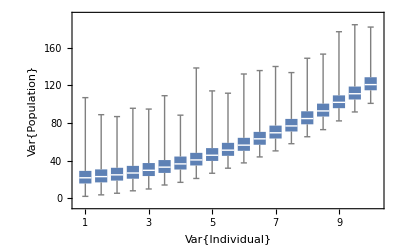

```mathematica
BoxWhiskerChart[VarMix,ChartStyle->ColorData[97,1],ChartLabels->Table[If[Mod[x,IntegerPart[x]]==0,IntegerPart[x],""],{x,1,10,0.5}],
FrameLabel->{"Individual isotopic variance","Population isotopic variance"}]
```

```mathematica
Table[If[IntegerQ[x],ToString[x]," "],{x,1,10,0.5}]
```

{ , , , , , , , , , , , , , , , , , , }

```mathematica
ToInt[x_] :=If[IntegerQ[x],ToString[x],""]
```

```mathematica
Table[x,{x,1,10,0.5}]
```

{1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.}

```mathematica
ToInt/@Table[x,{x,1,10,0.5}]
```

{,,,,,,,,,,,,,,,,,,}

```mathematica
IntegerQ[1.0]
```

False

```mathematica
Mod[1.5,IntegerPart[1.5]]
```

0.5